```mathematica
NS[];
```

```mathematica
ClearAll[diff];diff[o_,s_,f1_,f2_]:=PDF[MultinormalDistribution[DiagonalMatrix@Table[s^2,3-o]],Differences[{f1,1-f1-f2,f2},o]]
```

```mathematica
Log@diff[2,0.1,1/2,1/2]
```

-48.6164

```mathematica
Log@diff[2,0.1,f1,f2]
```

Log[3.98942 ⅇ^(-50. (-2+3 f1+3 f2)^2)]

```mathematica
Log@diff[2,0.1,1/3,1/3]
```

1.38365

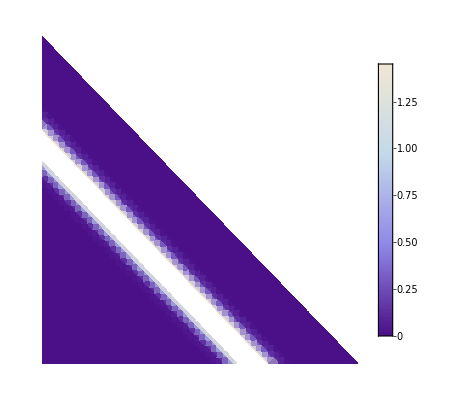

```mathematica
DensityPlot[diff[2,1/10,Rationalize@f1,Rationalize@f2],{f1,0,1},{f2,0,1},Mesh->None,RegionFunction->Function[{x,y},x+y≤1],AspectRatio->1,PlotLegends->Auto,ColorFunction->Auto(*mycolorfunction[#,-1]&*)]
```

```mathematica
ClearAll[diff];diff[o_,s_,f1_,f2_,f3_]:=PDF[MultinormalDistribution[DiagonalMatrix@Table[s^2,4-o]],Differences[{1-f1-f2-f3,f1,f2,f3},o]]
```

```mathematica
Log@diff[2,0.1,1/4,1/4,1/4]
```

2.76729

```mathematica
Log@diff[2,0.1,1/2,0,1/2]
```

-97.2327

```mathematica
ContourPlot3D[Log@diff[2,0.5,f1,f2,f3],{f1,0,1},{f2,0,1},{f3,0,1},Contours->10,Mesh->None,RegionFunction->Function[{x,y,z},x+y+z≤1],Axes->True,BoxRatios->1,PlotLegends->Auto,ColorFunction->mycolorfunction]
```

-Graphics3D-

```mathematica
DensityPlot3D[Log@diff[2,0.5,f1,f2,f3],{f1,0,1},{f2,0,1},{f3,0,1},RegionFunction->Function[{x,y,z},x+y+z≤1],Axes->True,BoxRatios->1]
```

```mathematica
ms=T[Differences[#,50]&/@IdentityMatrix[51]]
```

{{1,-50,1225,-19600,230300,-2118760,15890700,-99884400,536878650,-2505433700,10272278170,-37353738800,121399651100,-354860518600,937845656300,-2250829575120,4923689695575,-9847379391150,18053528883775,-30405943383200,47129212243960,-67327446062800,88749815264600,-108043253365600,121548660036300,-126410606437752,121548660036300,-108043253365600,88749815264600,-67327446062800,47129212243960,-30405943383200,18053528883775,-9847379391150,4923689695575,-2250829575120,937845656300,-354860518600,121399651100,-37353738800,10272278170,-2505433700,536878650,-99884400,15890700,-2118760,230300,-19600,1225,-50,1}}

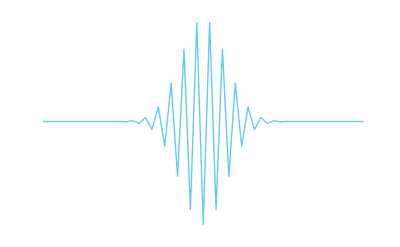

```mathematica
ListPlot[Flatten[ms],Joined->True,PlotRange->All]
```